This notebook is to study the effect of A for kinetic+rotation energy on length distribution.

```mathematica
gamma = 1.5
J=4
Jkrj=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-u×l))-1,{u,-0.0001}],{A,{1,10,100,1000,10000}},{x,0.1,20,0.1}]
```

1.5

4

{{6.52553,4.22203,3.09211,2.48552,2.09665,1.81315,1.59087,1.40901,1.25622,1.12555,1.01238,0.913449,0.826329,0.74917,0.680509,0.61917,0.564187,0.51476,0.470215,0.429981,0.39357,0.36056,0.330587,0.303332,0.278516,0.255895,0.235253,0.216396,0.199155,0.183378,0.168928,0.155686,0.14354,0.132394,0.122158,0.112753,0.104107,0.0961546,0.0888365,0.0820991,0.0758936,0.0701757,0.0649051,0.0600448,0.0555615,0.0514243,0.0476055,0.0440794,0.0408225,0.0378136,0.0350328,0.0324624,0.0300857,0.0278877,0.0258544,0.0239731,0.0222319,0.0206203,0.0191282,0.0177464,0.0164667,0.0152812,0.0141828,0.0131649,0.0122215,0.011347,0.0105363,0.00978451,0.00908733,0.00844068,0.00784083,0.0072843,0.00676791,0.00628871,0.00584395,0.00543112,0.00504788,0.00469207,0.00436169,0.00405489,0.00376996,0.00350532,0.00325949,0.00303111,0.00281894,0.00262179,0.0024386,0.00226835,0.00211012,0.00196303,0.00182627,0.00169908,0.0015807,0.00147043,0.00136756,0.00127139,0.00118126,0.00109652,0.00101654,0.00094077,0.000868672,0.000799784,0.000733691,0.000670027,0.000608476,0.000548766,0.00049066,0.000433956,0.00037848,0.000324085,0.000270641,0.000218039,0.000166184,0.000114996,0.0000644024,0.0000143435,-0.0000352344,-0.0000843776,-0.000133127,-0.000181517,-0.000229581,-0.000277344,-0.000324833,-0.000372068,-0.000419069,-0.000465854,-0.000512437,-0.000558832,-0.000605053,-0.000651111,-0.000697015,-0.000742775,-0.000788399,-0.000833896,-0.000879272,-0.000924534,-0.000969688,-0.00101474,-0.00105969,-0.00110455,-0.00114932,-0.00119401,-0.00123861,-0.00128314,-0.0013276,-0.00137198,-0.00141629,-0.00146054,-0.00150472,-0.00154885,-0.00159291,-0.00163692,-0.00168087,-0.00172477,-0.00176862,-0.00181242,-0.00185617,-0.00189988,-0.00194354,-0.00198715,-0.00203073,-0.00207426,-0.00211775,-0.00216121,-0.00220462,-0.002248,-0.00229134,-0.00233465,-0.00237792,-0.00242116,-0.00246437,-0.00250755,-0.00255069,-0.00259381,-0.00263689,-0.00267995,-0.00272297,-0.00276597,-0.00280895,-0.00285189,-0.00289481,-0.00293771,-0.00298058,-0.00302342,-0.00306624,-0.00310904,-0.00315182,-0.00319457,-0.0032373,-0.00328001,-0.0033227,-0.00336536,-0.00340801,-0.00345063,-0.00349324,-0.00353583,-0.00357839,-0.00362094,-0.00366347,-0.00370598},{8.81213,6.35209,4.81719,3.7695,3.07527,2.60628,2.26518,1.99937,1.78206,1.59873,1.44086,1.30302,1.18147,1.07355,0.9772,0.890836,0.813163,0.743116,0.679799,0.622452,0.570423,0.523146,0.480127,0.440936,0.40519,0.372555,0.34273,0.315451,0.290479,0.267603,0.246632,0.227394,0.209735,0.193518,0.178614,0.164912,0.152309,0.14071,0.130031,0.120195,0.111132,0.102777,0.0950739,0.087968,0.0814112,0.0753591,0.0697712,0.0646104,0.0598428,0.0554371,0.0513649,0.0475999,0.0441183,0.0408979,0.0379184,0.0351613,0.0326094,0.030247,0.0280595,0.0260337,0.0241573,0.022419,0.0208082,0.0193155,0.0179319,0.0166493,0.0154601,0.0143573,0.0133346,0.012386,0.0115059,0.0106895,0.00993184,0.00922875,0.00857618,0.00797044,0.0074081,0.00688601,0.00640121,0.00595101,0.0055329,0.00514454,0.00478379,0.00444865,0.00413727,0.00384795,0.0035791,0.00332925,0.00309704,0.0028812,0.00268057,0.00249406,0.00232065,0.00215943,0.0020095,0.00187007,0.00174034,0.0016196,0.00150712,0.00140221,0.00130418,0.00121236,0.00112611,0.00104479,0.000967843,0.000894721,0.000824945,0.000758086,0.000693767,0.000631656,0.000571468,0.000512957,0.00045591,0.000400145,0.000345506,0.000291858,0.000239086,0.000187091,0.000135787,0.0000851004,0.0000349665,-0.0000146702,-0.0000638582,-0.00011264,-0.000161053,-0.000209129,-0.000256898,-0.000304385,-0.000351612,-0.0003986,-0.000445367,-0.000491928,-0.000538298,-0.000584491,-0.000630517,-0.000676388,-0.000722113,-0.000767701,-0.000813159,-0.000858495,-0.000903716,-0.000948828,-0.000993836,-0.00103875,-0.00108356,-0.00112829,-0.00117293,-0.00121749,-0.00126197,-0.00130638,-0.00135072,-0.00139498,-0.00143919,-0.00148332,-0.0015274,-0.00157142,-0.00161538,-0.00165929,-0.00170315,-0.00174695,-0.0017907,-0.00183441,-0.00187807,-0.00192169,-0.00196526,-0.00200879,-0.00205228,-0.00209573,-0.00213914,-0.00218251,-0.00222585,-0.00226915,-0.00231241,-0.00235565,-0.00239885,-0.00244201,-0.00248515,-0.00252825,-0.00257133,-0.00261437,-0.00265739,-0.00270038,-0.00274334,-0.00278627,-0.00282918,-0.00287206,-0.00291492,-0.00295775,-0.00300056,-0.00304335,-0.00308611,-0.00312885,-0.00317157,-0.00321426,-0.00325694,-0.00329959,-0.00334222,-0.00338483,-0.00342743,-0.00347},{11.1131,8.63562,7.0278,5.79151,4.79025,3.9877,3.3715,2.90983,2.55726,2.27691,2.04527,1.84819,1.67699,1.52612,1.39185,1.27149,1.16308,1.06506,0.976201,0.895465,0.821985,0.755015,0.693904,0.638081,0.587042,0.540337,0.497566,0.458371,0.42243,0.389452,0.359175,0.331365,0.305807,0.282308,0.260692,0.240799,0.222485,0.205618,0.190078,0.175755,0.162549,0.15037,0.139133,0.128763,0.11919,0.110351,0.102186,0.0946432,0.0876725,0.0812293,0.0752721,0.0697631,0.0646674,0.0599531,0.0555906,0.051553,0.0478152,0.0443545,0.0411496,0.0381812,0.0354314,0.0328835,0.0305224,0.0283342,0.0263057,0.0244251,0.0226813,0.0210642,0.0195644,0.0181731,0.0168824,0.0156848,0.0145734,0.013542,0.0125847,0.0116961,0.0108711,0.0101051,0.00939382,0.00873327,0.00811978,0.00754994,0.00702059,0.00652881,0.0060719,0.00564734,0.00525282,0.00488617,0.00454539,0.00422865,0.00393421,0.00366049,0.00340601,0.0031694,0.0029494,0.00274481,0.00255455,0.0023776,0.00221302,0.00205993,0.00191751,0.00178497,0.0016616,0.00154666,0.00143949,0.00133938,0.00124568,0.00115773,0.00107491,0.000996632,0.000922349,0.000851564,0.000783833,0.000718763,0.000656008,0.00059527,0.000536288,0.00047884,0.000422734,0.000367806,0.000313913,0.000260935,0.000208766,0.000157316,0.000106509,0.0000562751,6.55689×10^-6,-0.0000426968,-0.0000915305,-0.000139983,-0.000188089,-0.000235879,-0.000283378,-0.000330611,-0.000377599,-0.00042436,-0.000470911,-0.000517268,-0.000563442,-0.000609448,-0.000655295,-0.000700994,-0.000746553,-0.000791981,-0.000837285,-0.000882473,-0.00092755,-0.000972523,-0.0010174,-0.00106217,-0.00110686,-0.00115147,-0.00119599,-0.00124043,-0.0012848,-0.00132909,-0.00137332,-0.00141748,-0.00146158,-0.00150562,-0.0015496,-0.00159352,-0.00163738,-0.0016812,-0.00172496,-0.00176868,-0.00181234,-0.00185596,-0.00189954,-0.00194307,-0.00198656,-0.00203001,-0.00207342,-0.00211679,-0.00216013,-0.00220342,-0.00224669,-0.00228991,-0.00233311,-0.00237627,-0.0024194,-0.00246249,-0.00250556,-0.0025486,-0.00259161,-0.00263459,-0.00267754,-0.00272047,-0.00276337,-0.00280624,-0.00284909,-0.00289191,-0.00293471,-0.00297748,-0.00302024,-0.00306296,-0.00310567,-0.00314835,-0.00319102,-0.00323366},{13.4155,10.9363,9.32075,8.06043,6.99823,6.06848,5.24359,4.51813,3.89937,3.39248,2.98732,2.66207,2.39488,2.16943,1.97474,1.8036,1.65122,1.51429,1.39045,1.27795,1.17541,1.08173,0.996021,0.917494,0.845481,0.77939,0.718698,0.662934,0.611672,0.564531,0.521161,0.481246,0.444499,0.410656,0.379479,0.350748,0.324264,0.299844,0.277321,0.256542,0.237366,0.219667,0.203324,0.188232,0.174292,0.161411,0.149507,0.138504,0.128332,0.118925,0.110224,0.102174,0.0947265,0.0878338,0.0814538,0.0755473,0.0700781,0.0650132,0.0603217,0.0559755,0.0519485,0.0482168,0.0447581,0.041552,0.0385797,0.0358238,0.033268,0.0308977,0.028699,0.0266593,0.0247668,0.0230108,0.0213811,0.0198686,0.0184646,0.0171613,0.0159512,0.0148276,0.0137842,0.0128152,0.0119152,0.0110792,0.0103026,0.00958103,0.00891064,0.00828771,0.00770882,0.00717082,0.00667078,0.00620599,0.00577392,0.00537225,0.00499881,0.00465159,0.00432872,0.00402849,0.00374927,0.00348959,0.00324806,0.00302339,0.00281441,0.00261999,0.00243912,0.00227084,0.00211426,0.00196856,0.00183294,0.00170667,0.00158905,0.00147938,0.00137699,0.0012812,0.00119138,0.00110688,0.00102712,0.000951542,0.000879624,0.000810911,0.000744991,0.000681506,0.00062014,0.00056062,0.000502712,0.000446213,0.000390948,0.000336769,0.000283547,0.000231172,0.000179547,0.000128591,0.0000782335,0.0000284114,-0.0000209285,-0.0000698331,-0.000118343,-0.000166495,-0.00021432,-0.000261846,-0.000309098,-0.000356098,-0.000402865,-0.000449417,-0.00049577,-0.000541937,-0.00058793,-0.000633763,-0.000679444,-0.000724983,-0.000770389,-0.000815669,-0.000860831,-0.000905881,-0.000950824,-0.000995667,-0.00104042,-0.00108507,-0.00112964,-0.00117413,-0.00121854,-0.00126287,-0.00130713,-0.00135133,-0.00139545,-0.00143951,-0.00148351,-0.00152746,-0.00157134,-0.00161517,-0.00165895,-0.00170268,-0.00174635,-0.00178998,-0.00183357,-0.00187711,-0.0019206,-0.00196406,-0.00200747,-0.00205084,-0.00209418,-0.00213748,-0.00218074,-0.00222397,-0.00226716,-0.00231032,-0.00235344,-0.00239654,-0.0024396,-0.00248263,-0.00252564,-0.00256861,-0.00261156,-0.00265448,-0.00269737,-0.00274024,-0.00278308,-0.00282589,-0.00286868,-0.00291145,-0.00295419,-0.00299691},{15.7181,13.2387,11.6224,10.3596,9.29089,8.34567,7.48712,6.69476,5.95803,5.2741,4.64727,4.08756,3.60513,3.20186,2.86867,2.59117,2.35578,2.15208,1.97274,1.81272,1.66849,1.53755,1.41807,1.30865,1.20822,1.11586,1.03083,0.952484,0.880259,0.81365,0.752199,0.695496,0.643162,0.594854,0.550255,0.509073,0.471042,0.435916,0.403467,0.373488,0.345786,0.320185,0.296521,0.274645,0.254418,0.235713,0.218413,0.20241,0.187605,0.173905,0.161226,0.14949,0.138626,0.128567,0.119252,0.110626,0.102635,0.0952319,0.0883728,0.0820168,0.076126,0.0706657,0.0656039,0.0609108,0.056559,0.0525232,0.04878,0.0453078,0.0420866,0.0390979,0.0363246,0.0337509,0.0313623,0.029145,0.0270867,0.0251758,0.0234015,0.0217538,0.0202237,0.0188026,0.0174826,0.0162564,0.0151172,0.0140588,0.0130754,0.0121615,0.0113123,0.010523,0.00978933,0.00910738,0.00847343,0.00788407,0.00733611,0.00682661,0.00635284,0.00591226,0.00550253,0.00512146,0.00476701,0.00443732,0.00413062,0.00384531,0.00357987,0.00333291,0.00310313,0.00288931,0.00269035,0.00250519,0.00233287,0.00217249,0.00202321,0.00188424,0.00175484,0.00163429,0.00152191,0.00141701,0.00131895,0.00122706,0.00114072,0.00105933,0.0009823,0.00090912,0.000839309,0.000772439,0.000708133,0.00064606,0.000585932,0.000527502,0.000470555,0.000414907,0.000360399,0.000306896,0.000254279,0.000202449,0.000151319,0.000100812,0.0000508632,1.41672×10^-6,-0.0000475773,-0.0000961621,-0.000144376,-0.000192251,-0.000239817,-0.000287101,-0.000334125,-0.000380909,-0.000427473,-0.000473831,-0.00052,-0.000565991,-0.000611817,-0.000657489,-0.000703015,-0.000748406,-0.00079367,-0.000838812,-0.000883841,-0.000928762,-0.000973582,-0.0010183,-0.00106293,-0.00110748,-0.00115194,-0.00119632,-0.00124062,-0.00128485,-0.00132901,-0.00137311,-0.00141714,-0.00146111,-0.00150502,-0.00154887,-0.00159267,-0.00163642,-0.00168011,-0.00172375,-0.00176735,-0.0018109,-0.00185441,-0.00189787,-0.00194129,-0.00198467,-0.00202801,-0.00207132,-0.00211458,-0.00215781,-0.00220101,-0.00224417,-0.00228729,-0.00233039,-0.00237345,-0.00241648,-0.00245948,-0.00250245,-0.0025454,-0.00258831,-0.0026312,-0.00267406,-0.0027169,-0.00275971}}

```mathematica
A1 = Jkrj[[1]]
A2 = Jkrj[[2]]
A3= Jkrj[[3]]
A4=Jkrj[[4]]
A5= Jkrj[[5]]
```

{6.52553,4.22203,3.09211,2.48552,2.09665,1.81315,1.59087,1.40901,1.25622,1.12555,1.01238,0.913449,0.826329,0.74917,0.680509,0.61917,0.564187,0.51476,0.470215,0.429981,0.39357,0.36056,0.330587,0.303332,0.278516,0.255895,0.235253,0.216396,0.199155,0.183378,0.168928,0.155686,0.14354,0.132394,0.122158,0.112753,0.104107,0.0961546,0.0888365,0.0820991,0.0758936,0.0701757,0.0649051,0.0600448,0.0555615,0.0514243,0.0476055,0.0440794,0.0408225,0.0378136,0.0350328,0.0324624,0.0300857,0.0278877,0.0258544,0.0239731,0.0222319,0.0206203,0.0191282,0.0177464,0.0164667,0.0152812,0.0141828,0.0131649,0.0122215,0.011347,0.0105363,0.00978451,0.00908733,0.00844068,0.00784083,0.0072843,0.00676791,0.00628871,0.00584395,0.00543112,0.00504788,0.00469207,0.00436169,0.00405489,0.00376996,0.00350532,0.00325949,0.00303111,0.00281894,0.00262179,0.0024386,0.00226835,0.00211012,0.00196303,0.00182627,0.00169908,0.0015807,0.00147043,0.00136756,0.00127139,0.00118126,0.00109652,0.00101654,0.00094077,0.000868672,0.000799784,0.000733691,0.000670027,0.000608476,0.000548766,0.00049066,0.000433956,0.00037848,0.000324085,0.000270641,0.000218039,0.000166184,0.000114996,0.0000644024,0.0000143435,-0.0000352344,-0.0000843776,-0.000133127,-0.000181517,-0.000229581,-0.000277344,-0.000324833,-0.000372068,-0.000419069,-0.000465854,-0.000512437,-0.000558832,-0.000605053,-0.000651111,-0.000697015,-0.000742775,-0.000788399,-0.000833896,-0.000879272,-0.000924534,-0.000969688,-0.00101474,-0.00105969,-0.00110455,-0.00114932,-0.00119401,-0.00123861,-0.00128314,-0.0013276,-0.00137198,-0.00141629,-0.00146054,-0.00150472,-0.00154885,-0.00159291,-0.00163692,-0.00168087,-0.00172477,-0.00176862,-0.00181242,-0.00185617,-0.00189988,-0.00194354,-0.00198715,-0.00203073,-0.00207426,-0.00211775,-0.00216121,-0.00220462,-0.002248,-0.00229134,-0.00233465,-0.00237792,-0.00242116,-0.00246437,-0.00250755,-0.00255069,-0.00259381,-0.00263689,-0.00267995,-0.00272297,-0.00276597,-0.00280895,-0.00285189,-0.00289481,-0.00293771,-0.00298058,-0.00302342,-0.00306624,-0.00310904,-0.00315182,-0.00319457,-0.0032373,-0.00328001,-0.0033227,-0.00336536,-0.00340801,-0.00345063,-0.00349324,-0.00353583,-0.00357839,-0.00362094,-0.00366347,-0.00370598}

{8.81213,6.35209,4.81719,3.7695,3.07527,2.60628,2.26518,1.99937,1.78206,1.59873,1.44086,1.30302,1.18147,1.07355,0.9772,0.890836,0.813163,0.743116,0.679799,0.622452,0.570423,0.523146,0.480127,0.440936,0.40519,0.372555,0.34273,0.315451,0.290479,0.267603,0.246632,0.227394,0.209735,0.193518,0.178614,0.164912,0.152309,0.14071,0.130031,0.120195,0.111132,0.102777,0.0950739,0.087968,0.0814112,0.0753591,0.0697712,0.0646104,0.0598428,0.0554371,0.0513649,0.0475999,0.0441183,0.0408979,0.0379184,0.0351613,0.0326094,0.030247,0.0280595,0.0260337,0.0241573,0.022419,0.0208082,0.0193155,0.0179319,0.0166493,0.0154601,0.0143573,0.0133346,0.012386,0.0115059,0.0106895,0.00993184,0.00922875,0.00857618,0.00797044,0.0074081,0.00688601,0.00640121,0.00595101,0.0055329,0.00514454,0.00478379,0.00444865,0.00413727,0.00384795,0.0035791,0.00332925,0.00309704,0.0028812,0.00268057,0.00249406,0.00232065,0.00215943,0.0020095,0.00187007,0.00174034,0.0016196,0.00150712,0.00140221,0.00130418,0.00121236,0.00112611,0.00104479,0.000967843,0.000894721,0.000824945,0.000758086,0.000693767,0.000631656,0.000571468,0.000512957,0.00045591,0.000400145,0.000345506,0.000291858,0.000239086,0.000187091,0.000135787,0.0000851004,0.0000349665,-0.0000146702,-0.0000638582,-0.00011264,-0.000161053,-0.000209129,-0.000256898,-0.000304385,-0.000351612,-0.0003986,-0.000445367,-0.000491928,-0.000538298,-0.000584491,-0.000630517,-0.000676388,-0.000722113,-0.000767701,-0.000813159,-0.000858495,-0.000903716,-0.000948828,-0.000993836,-0.00103875,-0.00108356,-0.00112829,-0.00117293,-0.00121749,-0.00126197,-0.00130638,-0.00135072,-0.00139498,-0.00143919,-0.00148332,-0.0015274,-0.00157142,-0.00161538,-0.00165929,-0.00170315,-0.00174695,-0.0017907,-0.00183441,-0.00187807,-0.00192169,-0.00196526,-0.00200879,-0.00205228,-0.00209573,-0.00213914,-0.00218251,-0.00222585,-0.00226915,-0.00231241,-0.00235565,-0.00239885,-0.00244201,-0.00248515,-0.00252825,-0.00257133,-0.00261437,-0.00265739,-0.00270038,-0.00274334,-0.00278627,-0.00282918,-0.00287206,-0.00291492,-0.00295775,-0.00300056,-0.00304335,-0.00308611,-0.00312885,-0.00317157,-0.00321426,-0.00325694,-0.00329959,-0.00334222,-0.00338483,-0.00342743,-0.00347}

{11.1131,8.63562,7.0278,5.79151,4.79025,3.9877,3.3715,2.90983,2.55726,2.27691,2.04527,1.84819,1.67699,1.52612,1.39185,1.27149,1.16308,1.06506,0.976201,0.895465,0.821985,0.755015,0.693904,0.638081,0.587042,0.540337,0.497566,0.458371,0.42243,0.389452,0.359175,0.331365,0.305807,0.282308,0.260692,0.240799,0.222485,0.205618,0.190078,0.175755,0.162549,0.15037,0.139133,0.128763,0.11919,0.110351,0.102186,0.0946432,0.0876725,0.0812293,0.0752721,0.0697631,0.0646674,0.0599531,0.0555906,0.051553,0.0478152,0.0443545,0.0411496,0.0381812,0.0354314,0.0328835,0.0305224,0.0283342,0.0263057,0.0244251,0.0226813,0.0210642,0.0195644,0.0181731,0.0168824,0.0156848,0.0145734,0.013542,0.0125847,0.0116961,0.0108711,0.0101051,0.00939382,0.00873327,0.00811978,0.00754994,0.00702059,0.00652881,0.0060719,0.00564734,0.00525282,0.00488617,0.00454539,0.00422865,0.00393421,0.00366049,0.00340601,0.0031694,0.0029494,0.00274481,0.00255455,0.0023776,0.00221302,0.00205993,0.00191751,0.00178497,0.0016616,0.00154666,0.00143949,0.00133938,0.00124568,0.00115773,0.00107491,0.000996632,0.000922349,0.000851564,0.000783833,0.000718763,0.000656008,0.00059527,0.000536288,0.00047884,0.000422734,0.000367806,0.000313913,0.000260935,0.000208766,0.000157316,0.000106509,0.0000562751,6.55689×10^-6,-0.0000426968,-0.0000915305,-0.000139983,-0.000188089,-0.000235879,-0.000283378,-0.000330611,-0.000377599,-0.00042436,-0.000470911,-0.000517268,-0.000563442,-0.000609448,-0.000655295,-0.000700994,-0.000746553,-0.000791981,-0.000837285,-0.000882473,-0.00092755,-0.000972523,-0.0010174,-0.00106217,-0.00110686,-0.00115147,-0.00119599,-0.00124043,-0.0012848,-0.00132909,-0.00137332,-0.00141748,-0.00146158,-0.00150562,-0.0015496,-0.00159352,-0.00163738,-0.0016812,-0.00172496,-0.00176868,-0.00181234,-0.00185596,-0.00189954,-0.00194307,-0.00198656,-0.00203001,-0.00207342,-0.00211679,-0.00216013,-0.00220342,-0.00224669,-0.00228991,-0.00233311,-0.00237627,-0.0024194,-0.00246249,-0.00250556,-0.0025486,-0.00259161,-0.00263459,-0.00267754,-0.00272047,-0.00276337,-0.00280624,-0.00284909,-0.00289191,-0.00293471,-0.00297748,-0.00302024,-0.00306296,-0.00310567,-0.00314835,-0.00319102,-0.00323366}

{13.4155,10.9363,9.32075,8.06043,6.99823,6.06848,5.24359,4.51813,3.89937,3.39248,2.98732,2.66207,2.39488,2.16943,1.97474,1.8036,1.65122,1.51429,1.39045,1.27795,1.17541,1.08173,0.996021,0.917494,0.845481,0.77939,0.718698,0.662934,0.611672,0.564531,0.521161,0.481246,0.444499,0.410656,0.379479,0.350748,0.324264,0.299844,0.277321,0.256542,0.237366,0.219667,0.203324,0.188232,0.174292,0.161411,0.149507,0.138504,0.128332,0.118925,0.110224,0.102174,0.0947265,0.0878338,0.0814538,0.0755473,0.0700781,0.0650132,0.0603217,0.0559755,0.0519485,0.0482168,0.0447581,0.041552,0.0385797,0.0358238,0.033268,0.0308977,0.028699,0.0266593,0.0247668,0.0230108,0.0213811,0.0198686,0.0184646,0.0171613,0.0159512,0.0148276,0.0137842,0.0128152,0.0119152,0.0110792,0.0103026,0.00958103,0.00891064,0.00828771,0.00770882,0.00717082,0.00667078,0.00620599,0.00577392,0.00537225,0.00499881,0.00465159,0.00432872,0.00402849,0.00374927,0.00348959,0.00324806,0.00302339,0.00281441,0.00261999,0.00243912,0.00227084,0.00211426,0.00196856,0.00183294,0.00170667,0.00158905,0.00147938,0.00137699,0.0012812,0.00119138,0.00110688,0.00102712,0.000951542,0.000879624,0.000810911,0.000744991,0.000681506,0.00062014,0.00056062,0.000502712,0.000446213,0.000390948,0.000336769,0.000283547,0.000231172,0.000179547,0.000128591,0.0000782335,0.0000284114,-0.0000209285,-0.0000698331,-0.000118343,-0.000166495,-0.00021432,-0.000261846,-0.000309098,-0.000356098,-0.000402865,-0.000449417,-0.00049577,-0.000541937,-0.00058793,-0.000633763,-0.000679444,-0.000724983,-0.000770389,-0.000815669,-0.000860831,-0.000905881,-0.000950824,-0.000995667,-0.00104042,-0.00108507,-0.00112964,-0.00117413,-0.00121854,-0.00126287,-0.00130713,-0.00135133,-0.00139545,-0.00143951,-0.00148351,-0.00152746,-0.00157134,-0.00161517,-0.00165895,-0.00170268,-0.00174635,-0.00178998,-0.00183357,-0.00187711,-0.0019206,-0.00196406,-0.00200747,-0.00205084,-0.00209418,-0.00213748,-0.00218074,-0.00222397,-0.00226716,-0.00231032,-0.00235344,-0.00239654,-0.0024396,-0.00248263,-0.00252564,-0.00256861,-0.00261156,-0.00265448,-0.00269737,-0.00274024,-0.00278308,-0.00282589,-0.00286868,-0.00291145,-0.00295419,-0.00299691}

{15.7181,13.2387,11.6224,10.3596,9.29089,8.34567,7.48712,6.69476,5.95803,5.2741,4.64727,4.08756,3.60513,3.20186,2.86867,2.59117,2.35578,2.15208,1.97274,1.81272,1.66849,1.53755,1.41807,1.30865,1.20822,1.11586,1.03083,0.952484,0.880259,0.81365,0.752199,0.695496,0.643162,0.594854,0.550255,0.509073,0.471042,0.435916,0.403467,0.373488,0.345786,0.320185,0.296521,0.274645,0.254418,0.235713,0.218413,0.20241,0.187605,0.173905,0.161226,0.14949,0.138626,0.128567,0.119252,0.110626,0.102635,0.0952319,0.0883728,0.0820168,0.076126,0.0706657,0.0656039,0.0609108,0.056559,0.0525232,0.04878,0.0453078,0.0420866,0.0390979,0.0363246,0.0337509,0.0313623,0.029145,0.0270867,0.0251758,0.0234015,0.0217538,0.0202237,0.0188026,0.0174826,0.0162564,0.0151172,0.0140588,0.0130754,0.0121615,0.0113123,0.010523,0.00978933,0.00910738,0.00847343,0.00788407,0.00733611,0.00682661,0.00635284,0.00591226,0.00550253,0.00512146,0.00476701,0.00443732,0.00413062,0.00384531,0.00357987,0.00333291,0.00310313,0.00288931,0.00269035,0.00250519,0.00233287,0.00217249,0.00202321,0.00188424,0.00175484,0.00163429,0.00152191,0.00141701,0.00131895,0.00122706,0.00114072,0.00105933,0.0009823,0.00090912,0.000839309,0.000772439,0.000708133,0.00064606,0.000585932,0.000527502,0.000470555,0.000414907,0.000360399,0.000306896,0.000254279,0.000202449,0.000151319,0.000100812,0.0000508632,1.41672×10^-6,-0.0000475773,-0.0000961621,-0.000144376,-0.000192251,-0.000239817,-0.000287101,-0.000334125,-0.000380909,-0.000427473,-0.000473831,-0.00052,-0.000565991,-0.000611817,-0.000657489,-0.000703015,-0.000748406,-0.00079367,-0.000838812,-0.000883841,-0.000928762,-0.000973582,-0.0010183,-0.00106293,-0.00110748,-0.00115194,-0.00119632,-0.00124062,-0.00128485,-0.00132901,-0.00137311,-0.00141714,-0.00146111,-0.00150502,-0.00154887,-0.00159267,-0.00163642,-0.00168011,-0.00172375,-0.00176735,-0.0018109,-0.00185441,-0.00189787,-0.00194129,-0.00198467,-0.00202801,-0.00207132,-0.00211458,-0.00215781,-0.00220101,-0.00224417,-0.00228729,-0.00233039,-0.00237345,-0.00241648,-0.00245948,-0.00250245,-0.0025454,-0.00258831,-0.0026312,-0.00267406,-0.0027169,-0.00275971}

General::munfl: Exp[-711.283] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-717.809] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.334] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

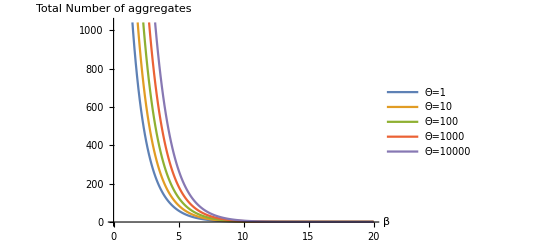

```mathematica
ListLinePlot[{(ⅇ^-A1+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A1×l))/(ⅇ^-A1+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A1×l))×10000,(ⅇ^-A2+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A2×l))/(ⅇ^-A2+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A2×l))×10000,(ⅇ^-A3+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A3×l))/(ⅇ^-A3+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A3×l))×10000,(ⅇ^-A4+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A4×l))/(ⅇ^-A4+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A4×l))×10000,(ⅇ^-A5+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A5×l))/(ⅇ^-A5+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A5×l))×10000},DataRange->{0,20},PlotLegends->{"Θ=1","Θ=10","Θ=100","Θ=1000","Θ=10000"},AxesLabel->{"β","Total Number of aggregates"}]
```

General::munfl: Exp[-711.283] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-717.809] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.334] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

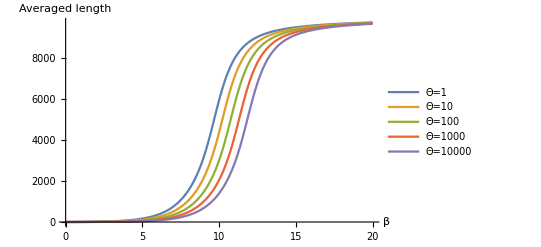

```mathematica
ListLinePlot[{(ⅇ^-A1+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A1×l))/(ⅇ^-A1+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A1×l)),(ⅇ^-A2+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A2×l))/(ⅇ^-A2+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A2×l)),(ⅇ^-A3+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A3×l))/(ⅇ^-A3+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A3×l)),(ⅇ^-A4+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A4×l))/(ⅇ^-A4+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A4×l)),(ⅇ^-A5+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-A5×l))/(ⅇ^-A5+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-A5×l))},DataRange->{0,20},PlotLegends->{"Θ=1","Θ=10","Θ=100","Θ=1000","Θ=10000"},AxesLabel->{"β","Averaged length"}]
```